```mathematica
Nt = 455(*551*) ;(*151*)
ti = 0; tf =15(*1*)(*5*); 
deltat = (tf - ti) /Nt ;
Nx = 455(*551*); (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = -30; xf = 30;(*-40 to 40*)
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

0.25

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
h = N[(2*Pi)/ (Nx),32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
X = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- (x)^2);

fexact[t_,x_] = ⅇ^(- ((x-t))^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Real];
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
```

```mathematica
D1 = N[((2*Pi)/(xf - xi))*Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];
```

```mathematica
(*LD2*)
ULD2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD2[[1,All]] = N[f[X],32];
ULD2 = N[ULD2,32];
ULD2 = Chop[ULD2, 10^(-307)];
ULD2 = Developer`ToPackedArray[ULD2, Real]; 
Developer`PackedArrayQ[ULD2]


ILD2 = N[IdentityMatrix[Length[D1]],32];
ALD2 = N[ILD2 - ((DL / 2)),32];
BLD2 = N[ILD2 + ((DL / 2)),32];
MLD2 = N[Inverse[ALD2].BLD2,32];
EMLD2 = N[MLD2 - ILD2,32];
EMLD2 = Developer`ToPackedArray[EMLD2, Real]; 

Do[ULD2[[n+1,All]] = ULD2[[n,All]] + (EMLD2 ).ULD2[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*RK2*)
URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[X],32];
URK2 = Chop[URK2, 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]

IRK2 = N[IdentityMatrix[Length[DL]],32];

MRK2 = N[(IRK2 + (DL) + ((1/2)*(MatrixPower[DL,2]))),32];

EMRK2 = N[MRK2 - IRK2,32];

EMRK2= Developer`ToPackedArray[EMRK2, Real]; 

Do[URK2[[n+1,All]] = URK2[[n,All]] + (EMRK2).URK2[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK4*)
URK4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK4[[1,All]] = N[f[X],32];
URK4 = Chop[URK4, 10^(-307)];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]

IRK4 = N[IdentityMatrix[Length[DL]],32];

MRK4 = N[IRK4 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4])),32];

EMRK4 = N[MRK4 - IRK4,32];

EMRK4= Developer`ToPackedArray[EMRK4, Real]; 

Do[URK4[[n+1,All]] = URK4[[n,All]] + (EMRK4).URK4[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD4*)
ULD4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD4[[1,All]] = N[f[X],32];
ULD4 = Chop[ULD4, 10^(-307)];
ULD4 = Developer`ToPackedArray[ULD4, Real]; 
Developer`PackedArrayQ[ULD4]


ILD4 = N[IdentityMatrix[Length[D1]],32];
ALD4 = N[ILD4 - ((DL / 2)) + (((MatrixPower[DL,2])/12)),32];
BLD4 = N[ILD4 + ((DL / 2)) + (((MatrixPower[DL,2])/12)),32];
MLD4 = N[Inverse[ALD4].BLD4,32];
EMLD4 = N[MLD4 - ILD4,32];

EMLD4= Developer`ToPackedArray[EMLD4, Real]; 

Do[ULD4[[n+1,All]] = ULD4[[n,All]] + (EMLD4).ULD4[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD6*)
ULD6= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD6[[1,All]] = N[f[X],32];
ULD6 = Chop[ULD6, 10^(-307)];
ULD6 = Developer`ToPackedArray[ULD6, Real]; 
Developer`PackedArrayQ[ULD6]


ILD6 = N[IdentityMatrix[Length[D1]],32];
ALD6 = N[ILD6 - ((DL / 2)) + (((MatrixPower[DL,2])/10)) - (((MatrixPower[DL,3])/120)),32];
BLD6 = N[ILD6 + ((DL / 2)) + (((MatrixPower[DL,2])/10)) + (((MatrixPower[DL,3])/120)),32];
MLD6 = N[Inverse[ALD6].BLD6,32];
EMLD6 = N[MLD6 - ILD6,32];

EMLD6= Developer`ToPackedArray[EMLD6, Real]; 

Do[ULD6[[n+1,All]] = ULD6[[n,All]] + (EMLD6).ULD6[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK6*)
URK6= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK6[[1,All]] = N[f[X],32];
URK6 = Chop[URK6, 10^(-307)];
URK6 = Developer`ToPackedArray[URK6, Real]; 
Developer`PackedArrayQ[URK6]

IRK6 = N[IdentityMatrix[Length[DL]],32];


MRK6 = N[IRK6 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4])) + ((1/120) * (MatrixPower[DL,5])) + ((1/720) * (MatrixPower[DL,6])),32];

EMRK6 = N[MRK6 - IRK6,32];

EMRK6= Developer`ToPackedArray[EMRK6, Real]; 

Do[URK6[[n+1,All]] = URK6[[n,All]] + (EMRK6).URK6[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD8*)
ULD8= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD8[[1,All]] = N[f[X],32];
ULD8 = Chop[ULD8, 10^(-307)];
ULD8 = Developer`ToPackedArray[ULD8, Real]; 
Developer`PackedArrayQ[ULD8]


ILD8 = N[IdentityMatrix[Length[D1]],32];
ALD8 = N[ILD8 - ((DL / 2)) + (((3*MatrixPower[DL,2])/28)) - (((MatrixPower[DL,3])/84)) + (((MatrixPower[DL,4])/1680)),32];
BLD8 = N[ILD8 + ((DL / 2)) + (((3*MatrixPower[DL,2])/28)) + (((MatrixPower[DL,3])/84)) + (((MatrixPower[DL,4])/1680)),32];
MLD8 = N[Inverse[ALD8].BLD8,32];
EMLD8 = N[MLD8 - ILD8,32];

EMLD8= Developer`ToPackedArray[EMLD8, Real]; 

Do[ULD8[[n+1,All]] = ULD8[[n,All]] + (EMLD8).ULD8[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*Now we don't need D1 or DL to have 32 digit accuracy so can put it into a packed array*)
D1 = Developer`ToPackedArray[D1, Real];
DL = Developer`ToPackedArray[DL, Real];
```

```mathematica
(************************************************************************************************************************)
(*Eigenvalues*)
(************************************************************************************************************************)
```

```mathematica
(*LD2*)
evalsLD2 = Eigenvalues[N[MLD2]];
realEvalsLD2 = Re[evalsLD2];
imagEvalsLD2 = Im[evalsLD2];
(*combinedEvals = Transpose[{realEvals,imagEvals}];*)
(*ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*RK2*)
evalsRK2 = Eigenvalues[N[MRK2]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
(*ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*RK4*)
evalsRK4 = Eigenvalues[N[MRK4]];
realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];
(*ListPlot[Transpose[{realEvalsRK4,imagEvalsRK4}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*LD4*)
evalsLD4 = Eigenvalues[N[MLD4]];
realEvalsLD4= Re[evalsLD4];
imagEvalsLD4 = Im[evalsLD4];
(*ListPlot[{Transpose[{realEvalsN,imagEvalsN}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*LD2*)
FLD2 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD2 = Developer`ToPackedArray[FLD2, Real];
intLD2 = Table[0,{i,1,Length[FLD2[[All,1]]]}];
intLD2 = Developer`ToPackedArray[intLD2, Real];
Do[
FLD2[[i]] = (D1.ULD2[[i,All]])^2;

intLD2[[i]] = (2π)/Nx Total[FLD2[[i,All]]]
,{i,1,Length[FLD2[[All,1]]]}];
```

```mathematica
(*RK2*)
FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
FRK2 = Developer`ToPackedArray[FRK2, Real];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
intRK2 = Developer`ToPackedArray[intRK2, Real];
Do[
FRK2[[i]] = (D1.URK2[[i,All]])^2;

intRK2[[i]] = (2π)/Nx Total[FRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK2}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*RK4*)
FRK4= Table[0,{i,1,Nt},{j,1,Nx}];
FRK4 = Developer`ToPackedArray[FRK4, Real];
intRK4 = Table[0,{i,1,Length[FRK4[[All,1]]]}];
intRK4 = Developer`ToPackedArray[intRK4, Real];
Do[
FRK4[[i]] = (D1.URK4[[i,All]])^2;

intRK4[[i]] = (2π)/Nx Total[FRK4[[i,All]]]
,{i,1,Length[FRK4[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK4}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*LD4*)
FLD4 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD4 = Developer`ToPackedArray[FLD4, Real];
intLD4 = Table[0,{i,1,Length[FLD4[[All,1]]]}];
intLD4 = Developer`ToPackedArray[intLD4, Real];
Do[
FLD4[[i]] = (D1.ULD4[[i,All]])^2;

intLD4[[i]] = (2π)/Nx Total[FLD4[[i,All]]]
,{i,1,Length[FLD4[[All,1]]]}];
(*ListPlot[{Transpose[{T,intN}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*LD6*)
FLD6 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD6 = Developer`ToPackedArray[FLD6, Real];
intLD6 = Table[0,{i,1,Length[FLD6[[All,1]]]}];
intLD6 = Developer`ToPackedArray[intLD6, Real];
Do[
FLD6[[i]] = (D1.ULD6[[i,All]])^2;

intLD6[[i]] = (2π)/Nx Total[FLD6[[i,All]]]
,{i,1,Length[FLD6[[All,1]]]}];
```

```mathematica
(*RK6*)
FRK6 = Table[0,{i,1,Nt},{j,1,Nx}];
FRK6 = Developer`ToPackedArray[FRK6, Real];
intRK6 = Table[0,{i,1,Length[FRK6[[All,1]]]}];
intRK6 = Developer`ToPackedArray[intRK6, Real];
Do[
FRK6[[i]] = (D1.URK6[[i,All]])^2;

intRK6[[i]] = (2π)/Nx Total[FRK6[[i,All]]]
,{i,1,Length[FRK6[[All,1]]]}];
```

```mathematica
(*LD8*)
FLD8 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD8 = Developer`ToPackedArray[FLD8, Real];
intLD8 = Table[0,{i,1,Length[FLD8[[All,1]]]}];
intLD8 = Developer`ToPackedArray[intLD8, Real];
Do[
FLD8[[i]] = (D1.ULD8[[i,All]])^2;

intLD8[[i]] = (2π)/Nx Total[FLD8[[i,All]]]
,{i,1,Length[FLD8[[All,1]]]}];
```

```mathematica
energyErrorLD2 = Abs[intLD2 - intLD2[[1]]];
energyErrorLD4 = Abs[intLD4 - intLD4[[1]]];
energyErrorRK2 = Abs[intRK2 - intRK2[[1]]];
energyErrorRK4 = Abs[intRK4 - intRK4[[1]]];
energyErrorLD6 = Abs[intLD6 - intLD6[[1]]];
energyErrorRK6 = Abs[intRK6 - intRK6[[1]]];
energyErrorLD8 = Abs[intLD8 - intLD8[[1]]];
```

```mathematica
(*LD2 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorLD2}], PlotRange->Full]*)
```

```mathematica
(*LD4 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorLD4}], PlotRange->Full]*)
```

```mathematica
(*RK2 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorRK2}], PlotRange->Full]*)
```

```mathematica
(*RK4 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorRK4}], PlotRange->Full]*)
```

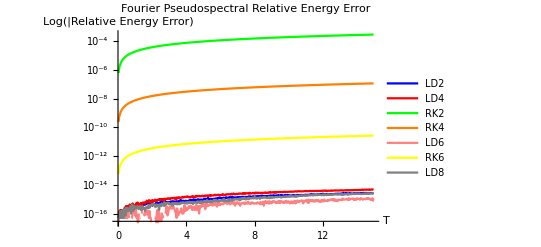

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}],Transpose[{T,energyErrorLD6}],Transpose[{T,energyErrorRK6}],Transpose[{T,energyErrorLD8}]},PlotStyle->{Blue, Red,Green, Orange,Pink,Yellow,Gray},PlotLegends->{"LD2","LD4","RK2","RK4","LD6","RK6","LD8"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Fourier Pseudospectral Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorRK4]}},Joined->True]
```

```mathematica
exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4,energyErrorLD6,energyErrorRK6,energyErrorLD8}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error_Pseudospectral_Final_Test.dat",exportData,"Table"];
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)
```

```mathematica
(*LD2*)
abserrLD2 = Abs[ULD2-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)
```

```mathematica
(*RK2*)
abserrRK2 = Abs[URK2-Uexact];
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
errorRK2 = Developer`ToPackedArray[errorRK2, Real];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

```mathematica
(*LD4*)
abserrLD4 = Abs[ULD4-Uexact];
errorLD4 = Table[0,{i,1,Length[abserrLD4]}];
errorLD4 = Developer`ToPackedArray[errorLD4, Real];
Do[
errorLD4[[i]] = Norm[abserrLD4[[i,All]], 1] * deltax;
,{i,1,Length[errorLD4]}
];
(*ListLinePlot[Transpose[{T,errorLD4}]]*)
```

```mathematica
(*RK4*)
abserrRK4 = Abs[URK4-Uexact];
errorRK4 = Table[0,{i,1,Length[abserrRK4]}];
errorRK4 = Developer`ToPackedArray[errorRK4, Real];
Do[
errorRK4[[i]] = Norm[abserrRK4[[i,All]], 1] * deltax;
,{i,1,Length[errorRK4]}
];
(*ListLinePlot[Transpose[{T,errorRK4}],PlotRange->All]*)
```

```mathematica
(*RK6*)
abserrRK6 = Abs[URK6-Uexact];
errorRK6 = Table[0,{i,1,Length[abserrRK6]}];
errorRK6 = Developer`ToPackedArray[errorRK6, Real];
Do[
errorRK6[[i]] = Norm[abserrRK6[[i,All]], 1] * deltax;
,{i,1,Length[errorRK6]}
];
```

```mathematica
(*LD6*)
abserrLD6 = Abs[ULD6-Uexact];
errorLD6 = Table[0,{i,1,Length[abserrLD6]}];
errorLD6 = Developer`ToPackedArray[errorLD6, Real];
Do[
errorLD6[[i]] = Norm[abserrLD6[[i,All]], 1] * deltax;
,{i,1,Length[errorLD6]}
];
```

```mathematica
(*LD8*)
abserrLD8 = Abs[ULD8-Uexact];
errorLD8 = Table[0,{i,1,Length[abserrLD8]}];
errorLD8 = Developer`ToPackedArray[errorLD8, Real];
Do[
errorLD8[[i]] = Norm[abserrLD8[[i,All]], 1] * deltax;
,{i,1,Length[errorLD8]}
];
```

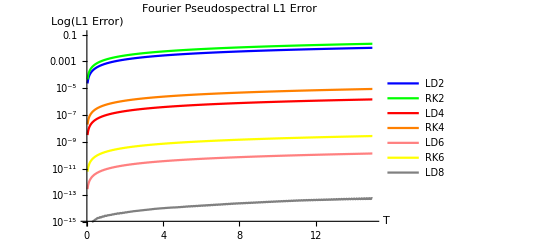

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}], Transpose[{T,errorRK2}], Transpose[{T,errorLD4}], Transpose[{T,errorRK4}],Transpose[{T,errorLD6}],Transpose[{T,errorRK6}],Transpose[{T,errorLD8}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-1}}, PlotStyle->{Blue,Green,Red,Orange,Pink,Yellow, Gray},PlotLegends->{"LD2","RK2","LD4","RK4","LD6","RK6","LD8"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```

```mathematica
(*ListLogPlot[{Transpose[{T,errorLD6}],Transpose[{T,errorRK6}],Transpose[{T,errorLD8}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-14}}, PlotStyle->{Blue,Green,Red},PlotLegends->{"LD6","RK6","LD8"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]*)
```

```mathematica
exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4,errorLD6,errorRK6,errorLD8}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Error_PS_Final_Test.dat",exportData,"Table"];
```

```mathematica
(*Animate[ListPlot[Table[ULD4[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
aniLD2 = Animate[ListLinePlot[{Transpose[{X,URK4[[n]]}],Transpose[{X,Uexact[[n]]}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{{xi,xf},{0,1}}], {n,1,Nt ,1} ]
```

```mathematica
Animate[ListLinePlot[Transpose[{X,(ULD2[[n]] - Uexact[[n]])}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]
```

```mathematica
(********************************************************************************************************************)
(*Start/Final*)
(********************************************************************************************************************)

(*exportData=Flatten/@Transpose[{X,LD2start, LD2startErr, LD2end, LD2endErr,RK2start, RK2startErr, RK2end, RK2endErr, LD4start, LD4startErr, LD4end, LD4endErr,RK4start, RK4startErr, RK4end, RK4endErr}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\start_final_PS.dat",exportData,"Table"];*)
```

```mathematica
(*Tutorial for way to eliminate roundoff error. paste inside a help window*)
(*tutorial/NDSolveSPRK#1464293172*)
```